```mathematica
ClearAll["Global`*"]
```

# Risk limiter functions

## Summary

## Soft knee downward limiter function

### Soft knee downward limiter function

h(x; b, c)=Piecewise[{{f(x; b, c)=1/(exp((log(b) (c x - 1)))+ (ⅇ c b log(b)) x, , for x<-1/(c log(b))≡a}, {g(x)=x, , for x>=-1/(c log(b))≡a}}]

f'(x)=d-c log(b) b^(1-c x)  
d=ⅇ c b log(b)+1

### Constraints

The constraints on the downward limiting multiplier are:

#### Constraints on x

x>=0 (because x is a standard deviation)

#### Constraints on b

0<b<1

#### Constraints on c

0<c<1/(b log(b) (ⅇ - b^(-c x_extreme))), x_extreme>-1/(c log(b))≡a

Equivalent:
0<c<1/(b log(b) (ⅇ - k_extreme)), k_extreme>ⅇ

k_extreme=b^(-c x_extreme)⇔x_extreme=-(log(k_extreme))/(c log(b))

x_extreme is the maximum possible value of x. Theoretically this value is ∞. In practice, this value is chosen heuristically. The trade-off is that the higher the x_extreme, the more narrow the valid range of c. For x_extreme=∞ there will be no valid value of c. For values of x_extreme very close to ⅇ, the max value of c can get very big, and the resulting h(x) may have negative slope for some values of x.

For b values close to 1, c can get very big. 

For implementation it can be a good idea to impose a maximum c value. Something like c=10 might be reasonable.

For implementation, we don’t know the minimum value of x_extreme, when we calculated the constraints on c. Instead we can calculate the constraints on c based on k_extreme, and then check that x_extreme>-1/(c log(b)).

### Plot

Note: In the following plots, for hard inequalities we set the range of c to [δ, c_max], and the range of b to [δ, b_max-δ], where δ=10^-12.

```mathematica
δ=1*^-8;
bmax =1; 
cmax=10;
(*xtreme=E+2;*) (*The higher the max x, the smaller the range of c*)

Clear[x,a,b,c]

(*aval[b_,c_,d_]:=1/c-log (d/(c log (b)))/(c log (b))*)
(*aval[x_,b_,c_]:=Solve[Log[b]*(1-c*x)-Log[x]==Log[-E*b*c Log[b]],x][[1]][[1]][[2]];*)
aval[b_, c_]:=-1/(c Log[b]);
(*tauzero[b_, γ_]:= γ * b*Log[b]*E;*)
(*tauinf[xtreme_, b_, γ_]:= γ * b*Log[b]*(E - b^(-γ*xtreme))*)
tauinf[kextreme_, b_, γ_]:= γ * b*Log[b]*(E - kextreme)

f[x_,b_,c_]:=1/(Exp[Log[b]*(c*x-1)])+ (E *b* c Log[b]+1)*x;
g[x_]:=x;
h[x_,b_,c_]:=Piecewise[{{f[x,b,c],x<aval[b,c]},{g[x],x>=aval[b,c]}}];

Manipulate[
LogLogPlot[h[x,b,c],
{x,δ,rangex},
AxesLabel->{"x","h(x)"},
PlotLabel->"Log-Log",
PlotRange->{{δ, rangex},Full}
],
{{b,0.1},δ,bmax-δ,Appearance->"Open"},
(*{{c, 0.1}, δ, If[b>1, 1/(b *Log[b]* E), cmax],Appearance->"Open"}*)
(*{{c, 0.1}, δ,If[b>1,NSolve[tauzero[b, γ]==1,γ,Reals][[1]][[1]][[2]],NSolve[tauinf[b, γ]==1,γ,Reals][[1]][[1]][[2]]],Appearance->"Open"}*)
(*{{c, 0.1}, δ, Min[1/(b*Log[b]*(E-xtreme)), cmax],Appearance->"Open"},*)
{{c, 0.1}, δ, Min[NSolve[tauinf[kextreme, b, γ]==1,γ,PositiveReals][[1]][[1]][[2]], cmax],Appearance->"Open"},
(*{{rangex, xtreme}, 2*δ, xtreme, Appearance->"Open"},*)
{{rangex, -Log[kextreme]/(c*Log[b])}, 2*δ, -Log[kextreme]/(c*Log[b]), Appearance->"Open"},
(*{xtreme, N[E+2]}*)
{kextreme, N[E+2]},
Dynamic[Style["x_extreme = " <>TextString[N[-Log[kextreme]/(c*Log[b])]], 12,If[kextreme>E,Blue, Red]]]
(*{{c,1/(2*Log[b]*(b-1))},δ, Min[maxc,1/(Log[b]*(b-1))-δ], Appearance->"Open"}*)
]
```

## Soft knee upward limiter function

### Soft knee downward limiter function

f(x; b, c) = b - (b - (b c - 1)/c)/(exp(c(x - (b c - 1)/c)))

f'(x)=c(b-(b c - 1)/c) exp(c((b c - 1)/c- x))

h(x)=Piecewise[{{f(x), for x>(b c - 1)/c}, {x, for 0<x<=(b c - 1)/c}}]

### Constraints

The constraints on the limiting multiplier are:

#### Constraints on x

x>=0 (because x is a standard deviation)

#### Constraints on b

b>0  because we take log of b (because b is a risk value, i.e. a standard deviation).
Given c, then b>1/c.

#### Constraints on c

c>1/b

## Plot

Constraint on x:
x>0

Constraint on b:
b>0

Constraint on c:
c>1/b

```mathematica
Clear[b, c, x]

bmax =10; 
cmax=20;

δ=1*^-12;
fup[x_, b_, c_]:=b-(b-((b * c-1)/c))/Exp[ c (x-((b * c-1)/c))]
gup[x_]:=x
hup[x_, b_, c_]:=Piecewise[{{fup[x, b, c], x>(b*c - 1)/c},{gup[x], x<=(b*c - 1)/c}}]

Manipulate[
Plot[
hup[x, b, c], 
{x,δ,rangex},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotRange->{{δ, rangex},Full}
],
{{b, 4}, δ, bmax, Appearance->"Open"},
{{c, 2}, 1/b+δ,cmax, Appearance->"Open"},
{{rangex, 10}, 2*δ, xmax, Appearance->"Open"},
{xmax, 10}
]
```

## Derivation

## Derivation of the downward limiter function

See derivation of the upward limiter function below.

We want to limit risk (standard deviation) downward.
Below x = a, limit y with a function, f, such that y approaches a limit, b, as x approaches 0 from above.
Above x = a, we want the input x to pass unchanged to the output y, i.e. g(x) = x. 
So we want to construct a piecewise function which is equal to f(x) below x = a and equal to g(x) above x = a.
Initial idea for f:

f(x) should tend to the limit b, as x tends to 0 from above.
f'(x) should tend to 0, as x tends to 0 from above.

This gives us the following idea:

f(x; a, b)=a/ⅇ^(log(b) (x-a))

f'(x; a, b)=-a log(b) b^(a-x)

Since g(x)=x, it must be true that in the point where f(x) meets g(x), f(a)=a.

```mathematica
f1[x_, a_, b_]:=a/(Exp[Log[b]*(x-a)])
```

Let’s set the limit to b = 0.5 and let f meet g in (1, 1).

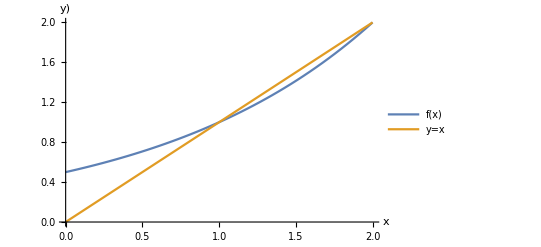

```mathematica
Plot[
{f1[x, 1, 0.5], x}, {x, 0, 2}, PlotRange->{0, 2},
PlotLegends->{"f(x)", "y=x"},
AxesLabel->{"x", "y)"}
]
```

f does meet g in (1, 1), but the combined curve will not be smooth.
And it won’t work for other values of a than 1!

Now, set a = 3:

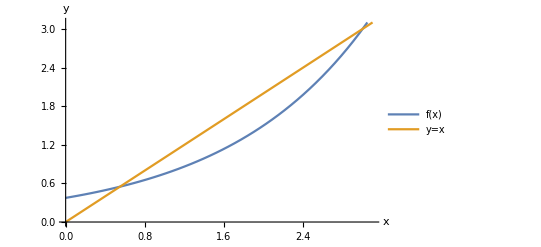

```mathematica
Plot[
{f1[x, 3, 0.5], x}, {x, 0, 3.1}, 
PlotRange->{0, 3.1},
PlotLegends->{"f(x)", "y=x"},
AxesLabel->{"x", "y"}
]
```

The blue line does not hit b at x=0:

f(x=0; a, b)=a/ⅇ^(log(b) (0 - a))=ab^a

So f(x) will only approach b from above when a=1.

We arrive at the soft knee limiter function

f(x)=1/(exp(log(b)  (c  x-1)))+ d x
with
f'(x)=d-c log(b) b^(1-c x)

We need to be able to set a fixed limit, b. Then by adjusting the “softness” of the knee and the horizontal “stretch” of the curve, it should be possible to find a point where g tangents f.
The x-value which we earlier called a, i.e. the x-value at which f(x) and g(x) meet, is now given implicitly by f(x). We will derive a below.

In this plot, c will stretch the blue curve, while d adjusts the softness of the knee:

```mathematica
Clear[x,b, c, d]
f6temp[x_, b_, c_, d_]:=1/( Exp[Log[b]*(c * x-1)])+d*x
df6[x_]=D[f6temp[x, b, c, d], x]
Manipulate[
LogLogPlot[
{f6temp[x, b, c , d], x}, 
{x, 0, 3},
PlotLegends->{"f(x)", "y=x"},
AxesLabel->{"x", "y"},
PlotLabel->"Log-log"
],
{{b, 0.1}, 0, 1, Appearance->"Open"},
{{c, 1}, 0.1, 10, Appearance->"Open"},
{{d, 0}, -1, 1, Appearance->"Open"}
]
```

d-c log(b) b^(1-c x)

f(x)=1/(exp( log(b) (c x - 1) ))+d x

f'(x)=d-c log(b) b^(1 - c x)

```mathematica
Clear[x,b,c,d]
f[x_,b_,c_,d_]:=1/(Exp[Log[b]*(c*x-1)])+d*x
df[x_]=D[f[x,b,c,d],x]
```

d-c log(b) b^(1-c x)

Find x for which f'(x; b, c, d)=1.

d-c log(b) b^(1-c x)=1

⇔c log(b) b^(1-c x)=d-1

⇔ b^(1-c x)=(d-1)/(c log(b))

⇔(1-c x)log(b)=log((d-1)/(c log(b)))

⇔1-c x=(log((d-1)/(c log(b))))/(log(b))

⇔x=1/c-(log((d-1)/(c log(b))))/(c log(b))

Find a for which f(x=a; b, c, d)=a.

1/(exp(log(b)(c x-1))))+d x=x

⇔1/(exp(log(b)(c x-1))))=(1-d)x

⇔exp(log(b)(1-c x)))=(1-d)x

⇔(exp(log(b)(1-c x))))/(1-d)=x

⇔log(b)(1-c x)-log(1-d)=log(x)

⇔log(b)(1-c x)-log(x)=log(1-d)

```mathematica
Clear[x, b, c, d]
aval[x_,b_,c_,d_]:=Solve[Log[b]*(1-c*x)-Log[x]==Log[1-d], x][[1]][[1]][[2]];
aval[x,b,c,d]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(W(-(b c log(b))/(d-1)))/(c log(b))

a=(W(-(b c log(b))/(d-1)))/(c log(b))

Set x=a and solve for d.

x = a
⇔1/c-(log((d-1)/(c log(b))))/(c log(b))=(W(-(b c log(b))/(d-1)))/(c log(b))

⇔log(b)-log((d-1)/(c log(b)))=W(-(b c log(b))/(d-1))

⇔d=ⅇ b c log(b)+1

```mathematica
Solve[Log[b]-Log[(d-1) / (c*Log[b])]==aval[x,b,c,d]*c*Log[b], d][[1]][[1]][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ⅇ b c log(b)+1

Plug the expression of d into the expression of a:

a=-1/(c log(b))

```mathematica
Clear[x, b, c]
aval[x_,b_,c_]:=Solve[Log[b]*(1-c*x)-Log[x]==Log[-E *b *c *Log[b]], x][[1]][[1]][[2]];
aval[x,b,c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-1/(c log(b))

We can now plot the final version of h, where

h(x; b, c)=Piecewise[{{f(x; b, c)=1/(exp((log(b) (c x - 1)))+ (ⅇ c b log(b)) x, , for x<-1/(c log(b))}, {g(x)=x, , for x>=-1/(c log(b))}}]

```mathematica
tauinf[b_, c_]:= c * b*Log[b]*(E - xtreme)
```

```mathematica
NSolve[tauinf[b, c]==1,c,Reals]
```

{{c→ConditionalExpression[-1./(b xtreme log(b)-2.71828 b log(b)), ]}}

```mathematica
δ=1*^-12;
maxc=10;(*Chosen maximum value of c (not theoretical max,which can be Inf for b=1).*)
maxx=E+2; (*The higher the max x, the smaller the range of c*)

Clear[x,a,b,c]

(*aval[b_,c_,d_]:=1/c-log (d/(c log (b)))/(c log (b))*)
(*aval[x_,b_,c_]:=Solve[Log[b]*(1-c*x)-Log[x]==Log[-E*b*c Log[b]],x][[1]][[1]][[2]];*)
aval[b_, c_]:=-1/(c Log[b]);
tauzero[b_, γ_]:= γ * b*Log[b]*E;
tauinf[b_, γ_]:= γ * b*Log[b]*(E - maxx);(*maxx = b^(-c*xtreme)*)

f[x_,b_,c_]:=1/(Exp[Log[b]*(c*x-1)])+ (E *b* c Log[b]+1)*x;
g[x_]:=x;
h[x_,b_,c_]:=Piecewise[{{f[x,b,c],x<aval[b,c]},{g[x],x>=aval[b,c]}}];

Manipulate[
LogLogPlot[h[x,b,c],
{x,0,1-δ},
AxesLabel->{"x","h(x)"},
PlotLabel->"Log-Log"],
{{b,0.1},δ,0.999,Appearance->"Open"},
(*{{c, 0.1}, δ, If[b>1, 1/(b *Log[b]* E), cmax],Appearance->"Open"}*)
{{c, 0.1}, δ,If[b>1,NSolve[tauzero[b, γ]==1,γ,Reals][[1]][[1]][[2]],NSolve[tauinf[b, γ]==1,γ,Reals][[1]][[1]][[2]]],Appearance->"Open"}
(*{{c,1/(2*Log[b]*(b-1))},δ, Min[maxc,1/(Log[b]*(b-1))-δ], Appearance->"Open"}*)
]
```

### Constraints

Finally, we need to calculate the valid parameter ranges for b and c, given x>=0.
These will be ones where f' is always positive for positive values of x.

So, we have f'(x)=d-c log(b) b^(1-c x)  and d=ⅇ b c log(b)+1, and we need:

d-c log(b) b^(1-c x)=ⅇ b c log(b)+1-c log(b) b^(1-c x)=c b log(b)(ⅇ -b^(-c x))+1> 0 
⟺c b log(b)(ⅇ -b^(-c x))< 1 

Let
τ(x; b, c):=c b log(b)(ⅇ -b^(-c x))

#### b>1

If b>1, then a=-1/(c log(b))<0, which means that h(x)=g(x)∀x>0. The softknee function will never kick in. So in implementation we should constrain b to 0<b<1.

Nevertheless, lets examine the case b>1.

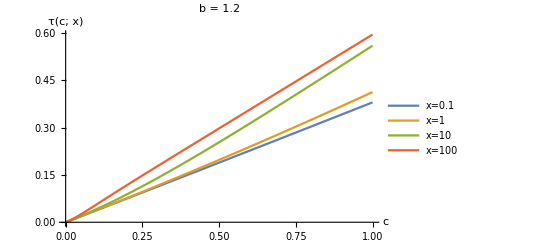

```mathematica
b = 1.2;
(*m=1; 
n=2*m+2;*)

Clear[c, x]

tauvals[x_, c_, b_]:= c*b*Log[b]*(E-b^(-c x))

(*xvalues=N[Flatten[Append[{0}, 10^(Range[-m,m])]]];*)

xvalues={0.1, 1, 10, 100};
n=Length[xvalues];

legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"x=",ToString[xvalues[[i]]]}]]
]

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[xvalues[[i]], c, b]]
]

Plot[
out,
{c, 0, 1},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->legends,
PlotLabel->StringJoin["b = ", ToString[b]]
]
```

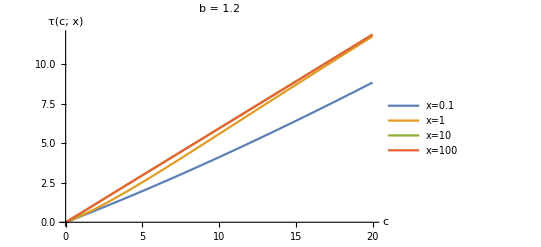

```mathematica
b = 1.2;
(*m=1; 
n=2*m+2;*)

Clear[c, x]

tauvals[x_, c_, b_]:= c*b*Log[b]*(E-b^(-c x))

(*xvalues=N[Flatten[Append[{0}, 10^(Range[-m,m])]]];*)

xvalues={0.1, 1, 10, 100};
n=Length[xvalues];

legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"x=",ToString[xvalues[[i]]]}]]
]

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[xvalues[[i]], c, b]]
]

Plot[
out,
{c, 0, 20},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->legends,
PlotLabel->StringJoin["b = ", ToString[b]]
]
```

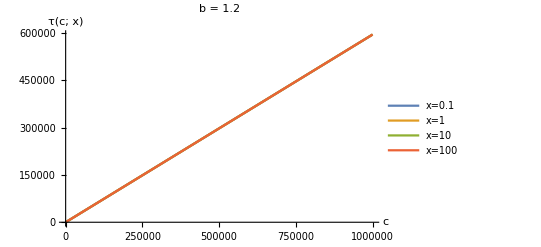

```mathematica
b = 1.2;
(*m=1; 
n=2*m+2;*)

Clear[c, x]

tauvals[x_, c_, b_]:= c*b*Log[b]*(E-b^(-c x))

(*xvalues=N[Flatten[Append[{0}, 10^(Range[-m,m])]]];*)

xvalues={0.1, 1, 10, 100};
n=Length[xvalues];

legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"x=",ToString[xvalues[[i]]]}]]
]

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[xvalues[[i]], c, b]]
]

Plot[
out,
{c, 0, 1000000},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->legends,
PlotLabel->StringJoin["b = ", ToString[b]]
]
```

τ(x; b, c)  is monotonically increasing in c for all values of x, when b>1.

Since we have an upper constraint on τ(x; b, c), the “worst case” is x=∞. As the plot suggests, the higher the value of x, the sooner τ(x; b, c) will reach the limit of 1, as c increases.

Look at the constraint again:

τ(x; b, c):=c b log(b)(ⅇ -b^(-c x))<1

For b>1 and c>0, -b^(-c x)->0 for x->∞, so c b log(b)(ⅇ -b^(-c x))->c b log(b)ⅇ.

In short:
τ(x; b, c)->c b log(b)ⅇ when x->∞ for all values of c.
τ(x; b, c) is increasing in c.

So the calculated max value of c will be the upper limit.

#### b>1, x=0

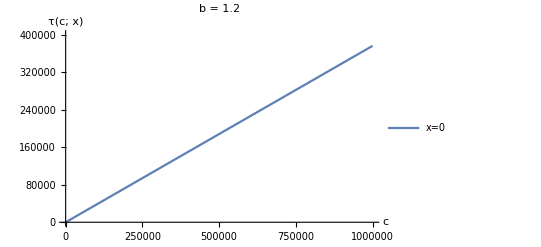

```mathematica
b = 1.2;
n=1;

Clear[c, x]

tauvals[x_, c_, b_]:= c*b*Log[b]*(E-b^(-c x))

xvalues={0};

legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"x=",ToString[xvalues[[i]]]}]]
]

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[xvalues[[i]], c, b]]
]

Plot[
out,
{c, -1, 1000000},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLabel->StringJoin["b = ", ToString[b]],
PlotLegends->legends,
PlotRange->{0, 400000}
]
```

For b>1 and x=0, τ(c; x)is increasing monotonically.

#### 0<b<1

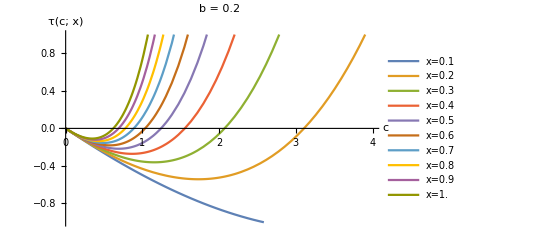

```mathematica
b = 0.2;
n=10;

Clear[c, x]

tauvals[x_, c_, b_]:= c*b*Log[b]*(E-b^(-c x))

xvalues=N[Range[1, n]/10];

legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"x=",ToString[xvalues[[i]]]}]]
]

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[xvalues[[i]], c, b]]
]

Plot[
out,
{c, 0, 4},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLabel->StringJoin["b = ", ToString[b]],
PlotLegends->legends,
PlotRange->{-1, 1}
]
```

τ(x; b, c)  is not monotonically increasing in c.

So for which extreme value of x should we solve τ(x; b, c) for c? 0 or ∞?

For positive values of τ(x; b, c), τ(x; b, c) is increasing in c, and τ(x; b, c) eventually exceeds 1 for all values of x, if we increase c enough.

Since we have an upper constraint on τ(x; b, c), the “worst case” is x=∞. As the plot suggests, the higher the value of x, the sooner τ(x; b, c) will reach the limit of 1, as c increases.

Look at the constraint again:

τ(x; b, c):=c b log(b)(ⅇ -b^(-c x))<1

For 0<b<1 and c>0, -b^(-c x)->-∞ for x->∞, and c b log(b)<0, so c b log(b)(ⅇ -b^(-c x))->∞.

In short:
τ(x; b, c)->∞ when x->∞ for all values of c.

In the extreme case, where x is extremely high, no value of c will be valid.
So we need to determine a practical range of x. For this we need heuristics.

#### 0<b<1, x=0

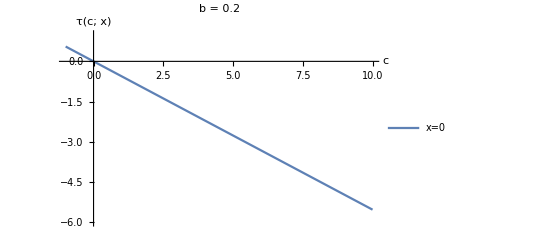

```mathematica
b = 0.2;
n=1;

Clear[c, x]

tauvals[x_, c_, b_]:= c*b*Log[b]*(E-b^(-c x))

xvalues={0};

legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"x=",ToString[xvalues[[i]]]}]]
]

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[xvalues[[i]], c, b]]
]

Plot[
out,
{c, -1, 10},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLabel->StringJoin["b = ", ToString[b]],
PlotLegends->legends,
PlotRange->{-6, 1}
]
```

For  0<b<1 and x=0, τ(c) is monitonically decreasing, and always negative for c>0.

### Implementation notes

For implementation, a way forward might be to solve τ(x; b, c)=1 for c given a value of b, to find the range of c where τ(x; b, c)<1.

τ(x; b, c):=c b log(b)(ⅇ -b^(-c x))<1

Given conditions b>0, x>0:

c b log(b)(ⅇ -b^(-c x))<1

⇔b log(b)(c ⅇ -c b^(-c x))<1

⇔(c ⅇ -c b^(-c x))<1/(b log(b)) for b log(b)>0⇔b>1

⇔(c ⅇ -c b^(-c x))>1/(b log(b)) for b log(b)<0⇔0<b<1

If 0<b<1, c should be greater than the calculated threshold.
If b<1, c should be less than the calculated threshold (and greater than 0).

We can’t solve this inequality analytically:

```mathematica
Clear[x, b, c]
b = 0.2;
Solve[c*E-c*b^(-c*x)==1/(b *Log[b]), c, Reals, Assumptions->{x>0, x<1}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[ⅇ c-c 0.2^(-c x)==-3.10667,c,ℝ,Assumptions→{x>0,x<1}]

```mathematica
Clear[x, b, c]
```

```mathematica
Solve[c*b*Log[b]* (E-b^(-c* x))<1, c, Reals, Assumptions->x>0]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[b c log(b) (ⅇ-b^(-c x))<1,c,ℝ,Assumptions→x>0]

WolframAlphaQueryNoResults

The strategy is to solve (c ⅇ -c b^(-c x))>1/(b log(b))for c with two extreme values of x.

#### b>1, x=0

First, we set x to 0:

τ(x; b, c):=c b log(b)(ⅇ -b^(-c x))<1

Let’s define τ(c):=τ(c; x, b)|_(x = ∞)=c b log(b)(ⅇ-1) 
for c>0.

Constraint:
c<1/(b log(b)(ⅇ-1))

Here we are imposing the constraint c>0, to simplify the problem.

```mathematica
Clear[x,b,c]
b=1.2;
x=0;

(*tauzero[b_, c_]:= c * b*Log[b]*(E-1)*)

(*NSolve[c*E-c*b^(-c*x)==1/(b*Log[b]),c,Reals]*)
(*NSolve[tauzero[b, c]==1,c,Reals]*)

1/( b*Log[b]*(E-1))
```

2.66003

So the constraint for b>1 and x=0 is:
c<2.66

But we already know from above, that the relevant extreme value of x is ∞.
So we can ignore this constraint.

#### b>1, x=∞

τ(x; b, c):=c b log(b)(ⅇ -b^(-c x))<1

Let’s define τ(c):=τ(c; x, b)|_(x = ∞)=c b log(b)ⅇ 

Constraint:
c<1/(b log(b)ⅇ)

```mathematica
tau2[b_, c_]:= c * b*Log[b]*E
```

```mathematica
Clear[x,b,c]
b=1.2;
x=0;

(*tauinf[b_, c_]:= c * b*Log[b]*E*)

(*NSolve[tauinf[b, c]==1,c,Reals]*)

1/ (b*Log[b]*E)
```

1.68146

So the constraint when b>1 and x=∞ is:
c<1.68

#### 0<b<1, x=0

τ(x; b, c):=c b log(b)(ⅇ -b^(-c x))<1

Let’s define τ(c):=τ(c; x, b)|_(x = ∞)=c b log(b)(ⅇ-1) 

Constraint:
c<1/(b log(b)(ⅇ-1))

```mathematica
Clear[x,b,c]
b=0.2;
x=0;

(*tauzero[b_, c_]:= c * b*Log[b]*(E-1)*)

(*NSolve[c*E-c*b^(-c*x)==1/(b*Log[b]),c,Reals]*)
(*NSolve[tauzero[b, c]==1,c,Reals]*)

1/(b*Log[b]*(E-1))
```

-1.80801

For  0<b<1 and x=0, τ(c) is monitonically decreasing, and always negative for c>0.

So ignoring the negative solution, there are no other constraints than

c>0

But again we already know from above, that the relevant extreme value of x is ∞.
So we can ignore this constraint, which is redundant anyway.

#### 0<b<1, x=∞

τ(x; b, c):=c b log(b)(ⅇ -b^(-c x))<1

Let’s define τ(c):=τ(c; x, b)|_(x = ∞)=c b log(b)(ⅇ-∞) 

Constraint:
c<1/(b log(b)(ⅇ-∞))

For implementation we replace the theoretical maximum possible x-value, ∞, with x_extreme. In practice, this value is chosen heuristically. The trade-off is that the higher the x_extreme, the more narrow the valid range of c. For x_extreme=∞ there will be no valid value of c. For values of x_extreme very close to ⅇ, the max value of c can get very big, and the resulting h(x) may have negative slope for some values of x.

For b values close to 1, c can get very big. 

For implementation it can be a good idea to impose a maximum c value. But this is a bit tricky, because the most useful value will depend on b.

We set x to a very high number which is effectly ∞. We find that x=1000000 is a reasonable extreme value:

```mathematica
Clear[x,b,c]
b=0.2;
xtreme=1000000;

(*tauinf[b_, c_]:= c * b*Log[b]*(E - xtreme)*)

(*NSolve[c*E-c*b^(-c*x)==1/(b*Log[b]),c,Reals]*)

(*NSolve[tauinf[b, c]==1,c,Reals]*)

1/( b*Log[b]*(E - xtreme))
```

3.10668×10^-6

τ(x; b, c)->∞ when x->∞ for all values of c.

This means that the max value of c goes to 0 when x->∞, for 0<b<1.

In the extreme case, where x is extremely high, no value of c will be valid.

So we need to determine a practical range of x. For this we need heuristics.

If the practical use case is x representing risk of daily returns as a standard deviation, a max x value of 1 should be extremely high. Let’s multiply that by 100. Let’s also pick a more realistic b value of 0.001.

```mathematica
Clear[x,b,c]
b=0.001;
xtreme=10;

(*tauinf[b_, c_]:= c * b*Log[b]*(E - xtreme)*)

(*NSolve[c*E-c*b^(-c*x)==1/(b*Log[b]),c,Reals]*)

(*NSolve[tauinf[b, c]==1,c,Reals]*)
1/( b*Log[b]*(E - xtreme))
```

19.8806

This gives us a maximum c value of 19.88.

```mathematica
Clear[x,b,c]
b=0.1;
xtreme=10;

tauinf[b_, c_]:= c * b*Log[b]*(E - b^(-c*xtreme))


cmax=NSolve[tauinf[b, c]==1,c,Reals][[2]][[1]][[2]];
cmax
b^(-cmax*xtreme)
```

0.150053

31.6611

## Derivation of the upward limiter function

We want to limit risk (standard deviation) upward.
Above x = a, limit y with a function, f, such that y approaches a limit, b, as x increases from below.
Below x = a, we want the input x to pass unchanged to the output y, i.e. y = x. 
Let g(x) = x.
So we want to construct a piecewise function which is equal to f above x = a and equal to g below x = a.
Initial idea for f:

f(x) should tend to the threshold b, as x tends to ∞.
f'(x) should tend to 0, as x tends to ∞.

This gives us the following idea:

f(x)=b-1/(exp(x))=b-exp(-x)

f'(x)=1/(exp(x))=exp(-x)

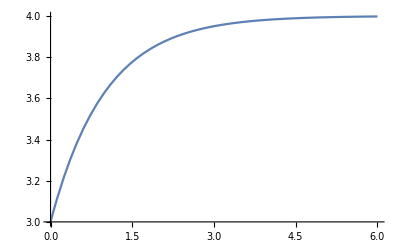

```mathematica
b=4;
Plot[
-Exp[-x]+b,
{x, 0, 6}
]
```

The plot suggests that we want to be able to shift the graph towards the right. For this we introduce a:

f(x)=b-1/(exp(x-a))=b-exp(a-x)

f'(x)=exp(a-x)

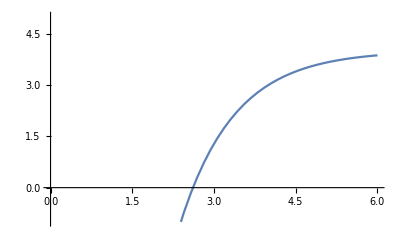

```mathematica
b=4;
a=4;
Plot[
b-Exp[a-x],
{x, 0, 6},
PlotRange->{-1,5}
]
```

As for the downward limiter, we also want to be able to change the shape of the knee. For this we introduce the variable c:

f(x; a, b, c)=b-1/(exp(c (x-a))=b-exp(c(a-x))

f'(x)= exp(c(a- x))

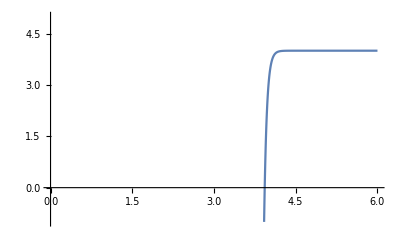

```mathematica
b=4;
a=4;
c=20;
k=2;
Plot[
b-Exp[c(a- x)],
{x, 0, 6},
PlotRange->{-1,5}
]
```

```mathematica
Clear[x,a, b, c]
(*f6temp[x_, b_, c_, d_]:=1/( Exp[Log[b]*(c * x-1)])+d*x*)
f7temp[x_, a_,b_, c_]:=b-Exp[c(a-x)]
Manipulate[
Plot[
{f7temp[x, a, b , c], x}, 
{x, 0, 6},
PlotLegends->{"f(x)", "y=x"},
PlotRange->{-2, 5},
AxesLabel->{"x", "y"}
],
{{a, 4}, 0.1, 10, Appearance->"Open"},
{{b,4}, 0.1, 10, Appearance->"Open"},
{{c, 2}, 1, 20, Appearance->"Open"}
]
```

Now we need to find the point where f(a)=a. At this point, g will touch f (though not necessarily be tangent). For this we modify f slightly:

f(x; a, b, c)=b-(b-a)/(exp(c (x-a)))

f'(x)=(b-a) exp(c(a- x))

We need to find the point where f' is 1 and f = g.

```mathematica
Clear[a, b, c]
f7temp2[x_, a_, b_, c_]:=b-(b-a)/Exp[ c (x-a)]
df7[x_]=D[f7temp2[x, a, b, c], x];
df7[x]

Solve[df7 [a]== 1, a]
```

c (b-a) ⅇ^(-c (x-a))

{{a→(b c-1)/c}}

We see that f'(x)=1 when a=(b c-1)/c.

We can now plug this expression of a into f, and join the piecewise functions at x=(b c-1)/c:

f(x; b, c) = b - (b - (b c - 1)/c)/(exp(c(x - (b c - 1)/c)))

f'(x)=c(b-(b c - 1)/c) exp(c((b c - 1)/c- x))

```mathematica
Clear[b, c, x]

f7[x_, b_, c_]:=b-(b-((b * c-1)/c))/Exp[ c (x-((b * c-1)/c))]
g7[x_]:=x
h7[x_, b_, c_]:=Piecewise[{{f7[x, b, c], x>(b*c - 1)/c},{g7[x], x<=(b*c - 1)/c}}]

Manipulate[
Plot[
h7[x, b, c], 
{x, 0,6}, 
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"}
],
{{b, 4}, 0.1, 10, Appearance->"Open"},
{{c, 2}, 0.1, 20, Appearance->"Open"}
]
```

### Constraints

And this works beatifully! We just need to find the valid parameter ranges for b and c.
These will be ones where f' is always positive for positive values of x.
So, we have f'(x)=(b-(b c - 1)/c) exp(c((b c - 1)/c- x)), which gives us the constraint:

(b-(b c - 1)/c) exp(c((b c - 1)/c- x))>0

Initial constraints:
1) x>0 (because x is a standard deviation)
2)  b c>1, because  a=(b c-1)/c<=0 for b c<=1.
3a) b>0  because we take log of b (because b is a risk value, i.e. a standard deviation).
3b) Given c, then b>1/c.
4a) Because b>0, then c>0, which follows from 2) and 3a).
4b) Given b, then c>1/b, which follows from 2) and 3).

exp(c((b c - 1)/c- x)) is always positive, so f'(x)>0, when b-(b c - 1)/c>0 ⟺b c>b c-1.
So there are no other constraints than the initial ones.

## Note on the product log function

To solve this problem we often run into situations where we need to solve equations of the general form
x ⅇ^x-1=0.
This has a solution which can not be expressed with elementary functions. The solution is the product log function – or Lambert W function.

See https://en.wikipedia.org/wiki/Lambert_W_function

## Scrap

f(x)=1/(exp(log(b)(c x-1))))+ (ⅇ c b log(b) + 1)x

f'(x)=c log(b)(1- b^(1-c x))+1

h(x)=Piecewise[{{f(x), for 0<x<1/c}, {x, for x>=1/c}}]

Downward softknee limiter

```mathematica
δ=1*^-12;
maxc=10; (*Chosen maximum value of c (not theoretical max, which can be Inf for b=1). *)
maxx=10;

f[x_, b_, c_]:=1/( Exp[Log[b]*(c * x-1)])+(c*Log[b]+1)*x
g[x_]:=x
h[x_, b_, c_]:=Piecewise[{{f[x, b, c], x<1/c},{g[x], x>=1/c}}]

Manipulate[
LogLogPlot[
h[x, b, c], 
{x, 0,10},
AxesLabel-> {"x", "h(x)"},
PlotLabel->"Log-Log"
],
{{b, 0.1}, δ, 10, Appearance->"Open"},
{{c, 1/(2*Log[b]*(b-1))},δ, Min[maxc, 1/(Log[b]*(b-1))-δ], Appearance->"Open"}
]
```

### Initial thoughts

See section “Our soft knee limiter function” below for analysis of the final limiter function.

We want to limit risk (standard deviation) downward.
Below x = a, limit y with a function, f, such that y approaches a limit, b, as x approaches 0 from above.
Above x = a, we want the input x to pass unchanged to the output y, i.e. y = x. 
Let g(x) = x.
So we want to construct a piecewise function which is equal to f below x = a and equal to g above x = a.
Initial idea for f:

f(x; a, b)=a/ⅇ^(log(b) (x-a))

```mathematica
f1[x_, a_, b_]:=a/(Exp[Log[b]*(x-a)])
```

Let’s set the limit to b = 0.5 and let f meet g in (1, 1).

```mathematica
Plot[
{f1[x, 1, 0.5], x}, {x, 0, 2}, PlotRange->{0, 2},
PlotLegends->{"f(x)", "y=x"},
AxesLabel->{"x", "y)"}
]
```

-Graphics-

f does meet g in (1, 1), but the combined curve will not be smooth.
And it won’t work for other values of a than 1!

Now, set a = 3:

```mathematica
Plot[
{f1[x, 3, 0.5], x}, {x, 0, 3.1}, 
PlotRange->{0, 3.1},
PlotLegends->{"f(x)", "y=x"},
AxesLabel->{"x", "y"}
]
```

-Graphics-

Again, f does meet g in (a, a), but the combined curve will not be smooth.
And what’s worse, the blue curve misses the minimum limit of 0.5!

Let’s try to construct a function that has g as a tangent. We can then join the two functions at the tangent point to get a smooth combined curve. So we want to find the derivative of f wrt x, i.e. the slope of f(x)...

f'(x; a, b)=-a log(b) b^(a-x)

```mathematica
df1[x_]=D[f1[x, a, b], x]
```

-a log(b) b^(a-x)

...and then we want to solve for a to figure out, for which expression of a the slope of f (x) is 1:

a=-1/(log(b))

```mathematica
Solve[df1[a]==1, a]
```

{{a→-1/(log(b))}}

We now substitute this expression of a into f(x):

f(x; b)=-1/(log(b)  exp(log(b) (x-(-1/(log(b))))))

```mathematica
f2[x_, b_]:=-1/(Log[b]*Exp[Log[b]*(x+(1/Log[b]))])
```

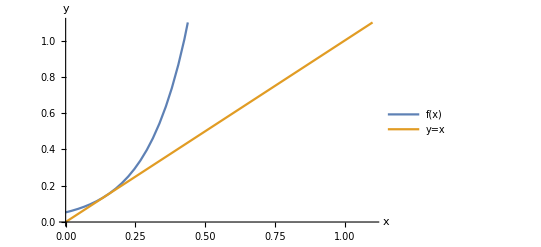

```mathematica
b =  0.001;

Plot[
{f2[x,b], x}, {x, 0, 1.1}, PlotRange->{0, 1.1},
PlotLegends->{"f(x)", "y=x"},
AxesLabel->{"x", "y"}
]
```

Instead of setting a manually, it is baked in as a property of f. The tangent point is at x = - 1/log(b):

```mathematica
-1/Log[b]
```

0.144765

But we still have the problem, that the blue curve is missing the limit value. (Which is only noticable in the plot for small balues of b, but  b will typically be small!)
Ignoring that, we can define the piecewise function h:

The value of f(0) is 0.053256, not 0.001 as it is supposed to be.

```mathematica
Limit[f2[x, b], x-> 0]
```

0.053256

We can show, that the limit is in fact a b^a – and not b. So we need to fix this.

```mathematica
a=-1/Log[b];
a*b^a
```

0.053256

```mathematica
f2[x_, b_]:=-1/(Log[b]*Exp[Log[b]*(x+(1/Log[b]))])
g2[x_]:=x
h2[x_, b_]:=Piecewise[{{f2[x, b], x<(-1/Log[b])},{g2[x], x>=(-1/Log[b])}}]
```

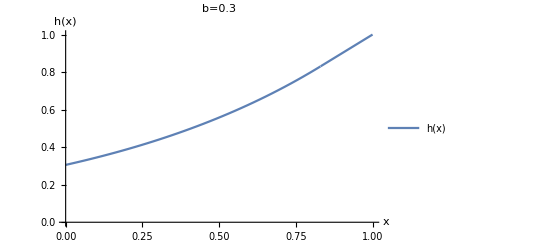

```mathematica
b = 0.3;

Plot[
h2[x, b], {x, 0, 1}, 
PlotRange->{0, 1},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotLabel->"b=0.3"
]
```

Notice: It looks like the curve hits the limit of 0.3. This is just luck!

Log-Log plot:

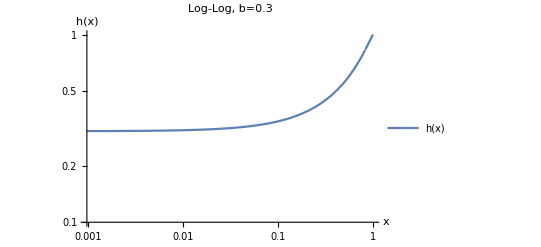

```mathematica
b = 0.3;

LogLogPlot[
h2[x, b], {x, 0, 1}, 
PlotRange->{0.1, 1},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotLabel->"Log-Log, b=0.3"
]
```

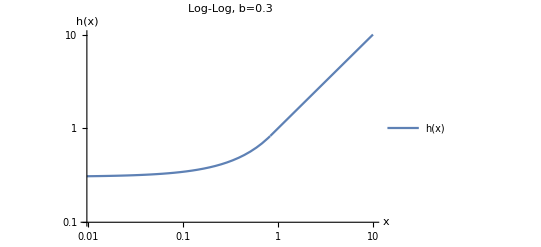

```mathematica
b = 0.3;

LogLogPlot[
h2[x, b],
{x, 0, 10}, 
PlotRange->{0.1, 10},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotLabel->"Log-Log, b=0.3"
]
```

Let’s try more realistic values:

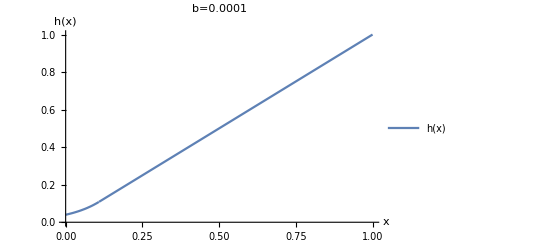

```mathematica
b = 0.0001;

Plot[
h2[x, b], 
{x, 0, 1}, 
PlotRange->{0, 1},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotLabel->"b=0.0001"
]
```

0.0001

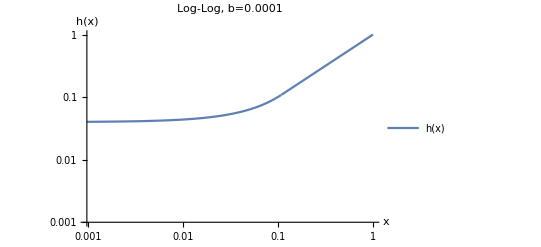

```mathematica
b = 0.0001

LogLogPlot[
h2[x, b], 
{x, 0, 1}, 
PlotRange->{0.001, 1},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotLabel->"Log-Log, b=0.0001"
]
```

Here it is plain to see, that we are missing the limit.

Where is the connection point (x = a)?

```mathematica
-1/Log[b]
```

0.108574

For a lower risk limit of 0.01%, the limiting function kicks in at σ=11%. That seems too high to be useful.

This is of course a trade-off between a sharp knee and a limit that kicks in at a high point. With a soft knee, basically all our risk calculations will be affected by the smoothing.

What if we try a much lower limit? This would not be something like a limit based on max leverage, but rather a sort of “absolute zero temperature” for all risk calculations in the system.

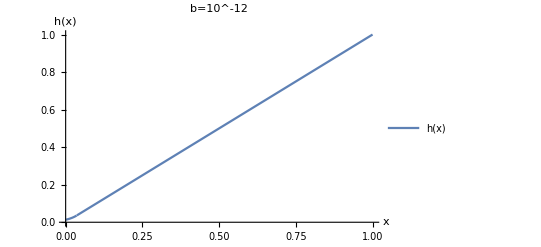

```mathematica
b = 1*^-12;

Plot[
h2[x, b], 
{x, 0, 1}, 
PlotRange->{0, 1},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotLabel->"b=10^-12"
]
```

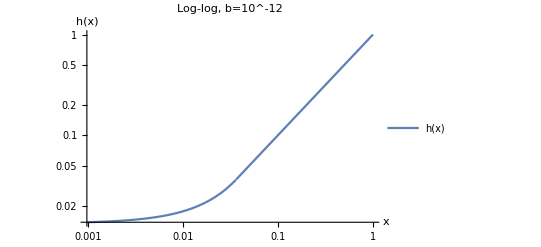

```mathematica
b = 1*^-12;

LogLogPlot[
h2[x, b], 
{x, 0, 1}, 
PlotRange->{0, 1},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotLabel->"Log-log, b=10^-12"
]
```

Connection point:

```mathematica
-1/Log[b]//N
```

0.0361912

Basically, moving the limit very close to 0 does help, but still affects risk values in the normal range.

Let’s try to make the knee adjustable. We introduce variable c (for “curvature, maybe...)

```mathematica
f3temp[x_, a_, b_, c_]:=a/( Exp[c*Log[b]*(x-a)])
```

```mathematica
Clear[a, b, c]
df3[x_]=D[f3temp[x, a, b, c], x]
```

-a c log(b) b^(-c (x-a))

...and then we want to solve for a to figure out, for which expression of a the slope of f(x) is 1:

```mathematica
Solve[df3[a]==1, a]
```

{{a→-1/(c log(b))}}

```mathematica
f3[x_,  b_, c_]:=-1/( c*Log[b]*Exp[c*Log[b]*(x+(1/(c*Log[b])))])
g3[x_]:=x
h3[x_, b_, c_]:=Piecewise[{{f3[x, b, c], x<(-1/(c*Log[b]))},{g3[x], x>=(-1/(c*Log[b]))}}]
```

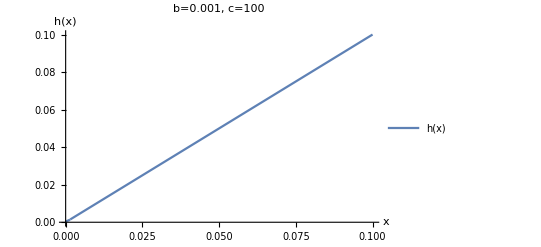

```mathematica
b = 0.001;
c = 100;

Plot[
h3[x, b, c], 
{x, 0,0.1}, 
PlotRange->{0, 0.1},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotLabel->"b=0.001, c=100"
]
```

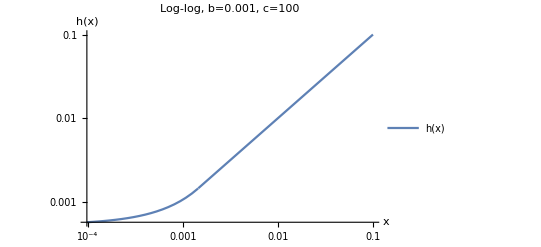

```mathematica
b = 0.001;
c = 100;

LogLogPlot[
h3[x, b, c], 
{x, 0,0.1}, 
PlotRange->{0, 0.1},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotLabel->"Log-log, b=0.001, c=100"
]
```

```mathematica
-1/(c*Log[b])
```

0.00144765

While the knee looks better, the limit is shifted downward.
What if we shift f upward to compensate?
Not surprisingly, the two lines won’t meet, when we shift on upward.
So not only must f'(4) = g'(4), we also need f(4) = g(4).

What if we multiply b by some factor, z. How could we then express z and a to meet the conditions?

```mathematica
Clear[a, b, c]
f4temp[x_, a_, b_, c_, z_]:=a/( Exp[c*Log[b*z]*(x-a)]) 
df4[x_]=D[f4temp[x, a,0.1, 10, z], x]
Solve[{df4[a]==1,f4temp[a, a, 0.1, 10, z]==a, f4temp[0, a,  0.1, 10, z]==0.1}, {a, z}]
```

23.0259 a 0.1^(-10 (x-a)) z^(-10 (x-a))-10 a 0.1^(-10 (x-a)) log(z) z^(-10 (x-a))

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[{23.0259 a-10. a log(z)==1,True,0.1^(10 a) a z^(10 a)==0.1},{a,z}]

Dead end...

```mathematica
f5[x_,  b_, c_]:=-1/( c*Log[b]*Exp[Log[b]*(c*x+(1/(c*Log[b])))])
g5[x_]:=x
h5[x_, b_, c_]:=Piecewise[{{f5[x, b, c], x<(-1/(c*Log[b]))},{g5[x], x>=(-1/(c*Log[b]))}}]

Manipulate[
LogLogPlot[
h5[x, b, c], 
{x, 0,1}, 
PlotRange->{0, 1},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"},
PlotLabel->"Log-log"
],
{{b, 0.1}, 0, 1, Appearance->"Open"},
{{c, 1}, 0.1, 10, Appearance->"Open"}
]
```

### Our final soft knee limiter function

We arrive at the soft knee limiter function

f(x)=1/(exp(log(b)  (c  x-1)))+ d x
with
f'(x)=d-c log(b) b^(1-c x)

```mathematica
Clear[x,b, c, d]
f6temp[x_, b_, c_, d_]:=1/( Exp[Log[b]*(c * x-1)])+d*x
df6[x_]=D[f6temp[x, b, c, d], x]
Manipulate[
LogLogPlot[
{f6temp[x, b, c , d], x}, 
{x, 0, 3},
PlotLegends->{"f(x)", "y=x"},
AxesLabel->{"x", "y"},
PlotLabel->"Log-log"
],
{{b, 0.1}, 0, 1, Appearance->"Open"},
{{c, 1}, 0.1, 10, Appearance->"Open"},
{{d, 0}, -1, 1, Appearance->"Open"}
]
```

d-c log(b) b^(1-c x)

We need to find the point where f' is 1 and f = g.

From f'(x)=d-c log(b) b^(1-c x) we immediately see that f'(x)=1 when c = 1/x and d=(log(b))/x+1. 
We now have two expressions of x:
x=1/c and x=(log(b))/(d-1), b>0, c>0, d≠0
⟺d=c log(b)+1

We can now plug this expression of d into f:

f(x)=1/(exp(log(b)(c x-1))))+ (c log(b) + 1)x

f'(x)=c log(b)(1- b^(1-c x))+1

The slope of this new f is 1 when

c log(b)(1- b^(1-c x))+1=1
⟺b^(1-c x)=1
⟺(1-c x) log(b)=0
⟺1-c x=0
⟺x=1/c

But 
f(1/c)=1+ log(b) + 1/c
which is not 1/c!

We need to get rid of the term 1+log(b). But if we just subtract it from f, we won’t hit the limit of bat x=0.

```mathematica
f6[x_, b_, c_]:=1/( Exp[Log[b]*(c * x-1)])+(c*Log[b]+1)*x
g6[x_]:=x
h6[x_, b_, c_]:=Piecewise[{{f6[x, b, c], x<1/c},{g6[x], x>=1/c}}]

Manipulate[
LogLogPlot[
h6[x, b, c], 
{x, 0,10}, 
PlotRange->{0, 10},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"}
],
{{b, 0.1}, 0, 1, Appearance->"Open"},
{{c, 0.1}, 0.01, 0.5, Appearance->"Open"}
]
```

The problem here is, that the two curves will only have the same slope at x = 1/c, which is not (necessarily) the point where the curves meet.

d-c log(b) b^(1-c x)=1
⟺

```mathematica
Clear[x, b, c, d]
f6temp[x_, b_, c_, d_]:=1/( Exp[Log[b]*(c * x-1)])+d*x
(*df6[x_]=D[f6temp[x, b, c, d], x]*)
df6[x_]=d - c*Log[b]*b^(1-c*x)
Solve[df6[x]==1, x]
```

d-c log(b) b^(1-c x)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(log(b)-log((d-1)/(c log(b))))/(c log(b))}}

d-c log(b) b^(1-c x)=1

⇔c log(b) b^(1-c x)=d-1

⇔ b^(1-c x)=(d-1)/(c log(b))

⇔(1-c x)log(b)=log((d-1)/(c log(b)))

⇔1-c x=(log((d-1)/(c log(b))))/(log(b))

⇔x=1/c-(log((d-1)/(c log(b))))/(c log(b))

f(x)=1/(exp(log(b)(c x-1))))+ (c log(b) + 1)x

f'(x)=c log(b)(1- b^(1-c x))+1

The slope of f is 1 when

c log(b)(1- b^(1-c x))+1=1
⟺b^(1-c x)=1
⟺(1-c x) log(b)=0
⟺1-c x=0
⟺x=1/c

f(0)=b as it is supposed to be.

But 
f(1/c)=1+ log(b) + 1/c
which is not 1/c!

This is ok:
f(x)=1/(exp(log(b)(c x-1))))

Adding a term creates the problem:
f(x)=1/(exp(log(b)(c x-1))))+dx

#### Constraints

Note: This section is based on a wrong expression of d!

This works. We just need to find the valid parameter ranges for b and c.
These will be ones where f' is always positive for positive values of x.
So, we have f'(x)=d-c log(b) b^(1-c x)  and d=c log(b)+1, and we need:

d-c log(b) b^(1-c x)=c log(b)+1-c log(b) b^(1-c x)=c log(b)(1- b^(1-c x))+1> 0 
⟺c log(b)( b^(1-c x)-1)< 1 

Let
τ(x; b, c):=c log(b)( b^(1-c x)-1)

1) b>0  because b is a risk value, i.e. a standard deviation, and because we take log of b.
2) x>0 (because x is a standard deviation)

We need to consider 4 regions of b, separated by the following values:

#### Region 1: 0<b<=1/ⅇ

∞<log(b)<=-1⟺0<b<=1/ⅇ 

If log(b)=-1, then b=1/ⅇ, and...
τ(x; b, c):=c b log(b)(ⅇ -b^(-c x)) <1

∞<log(b)<=-1⟺0<b<=1/ⅇ 

If log(b)=-1, then b=1/ⅇ, and...
τ(x; b, c):=c log(b)( b^(1-c x)-1)=c log(1/ⅇ)( (1/ⅇ)^(1-c x)-1)=-c( (1/ⅇ)^(1-c x)-1)=c(1- ⅇ^(c x-1))<1

This is not true for all values of c, when x is small.
(This is bad, because small values of  x are exactly the values we want to limit.)

Let’s define
τ(c; x):=c(1- ⅇ^(c x-1))

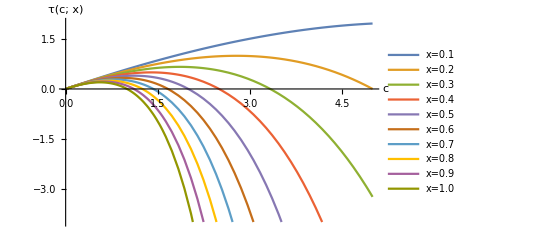

```mathematica
Plot[
{c(1- Exp[c* 0.1 -1]),
c(1- Exp[c * 0.2-1]),
c(1- Exp[c * 0.3-1]),
c(1- Exp[c * 0.4-1]),
c(1- Exp[c * 0.5-1]),
c(1- Exp[c* 0.6-1]),
c(1- Exp[c* 0.7-1]),
c(1- Exp[c* 0.8 -1]),
c(1- Exp[c* 0.9 -1]),
c(1- Exp[c* 1.0 -1])
},
{c, 0, 5},
PlotRange-> {-4, 2},
PlotLegends->{
"x=0.1",
"x=0.2",
"x=0.3",
"x=0.4",
"x=0.5",
"x=0.6",
"x=0.7",
"x=0.8",
"x=0.9",
"x=1.0"
},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]}
]
```

Let’s consider the extreme case where x=0:
Then we have the constraint
c(1- 1/ⅇ)<1
which is only true for c<ⅇ/(ⅇ- 1)≈1.58198

```mathematica
E/(E - 1)//N
```

1.58198

f(1.58)=1 looks about right.

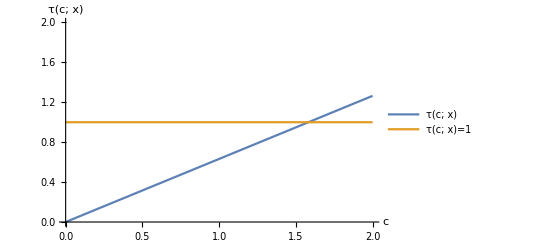

```mathematica
Clear[c]
Plot[
{c(1- Exp[-1]),
1
},
{c, 0, 2},
PlotRange-> {0, 2},
AxesLabel->{Style["c", 12], Style["τ(c; x)", 12] },
PlotLegends->{"τ(c; x)", "τ(c; x)=1"}
]
```

So far we have the constraint 0<c<1.58 for b=1/ⅇ.

What about for b=0?
If log(b)=0, then b=1, and...
τ(x; b, c):=c log(b)( b^(1-c x)-1)=0<1

...which is true for all c.

So what happens as we decrease b from a value of 1/ⅇ towards 0?

Going back to the constraint...
τ(x; b, c):=c log(b)( b^(1-c x)-1)<1

Let’s examine the LH side of the inequality as a function of b for different values of c.
We are setting x to 1.

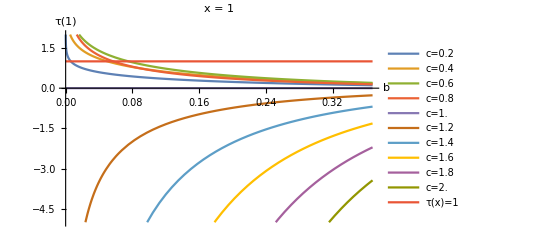

```mathematica
x=1;
n=10;

Clear[b, c]

tauvals[c_, b_]:= c*Log[b]*(b^(1-c)-1)

cvalues=N[(2*Range[1,n])/10];
legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"c=",ToString[cvalues[[i]]]}]]
]
legends=Append[legends, "τ(x)=1"];

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[cvalues[[i]], b]]
]
out=Append[out, 1];

Plot[
out,
{b, 0, 1/ⅇ},
PlotRange->{-5, 2},
PlotLegends-> legends,
AxesLabel-> {Style["b", 12],Style[StringJoin["τ(",ToString[x], ")"], 12] },
PlotLabel->StringJoin["x = ", ToString[x]]
]
```

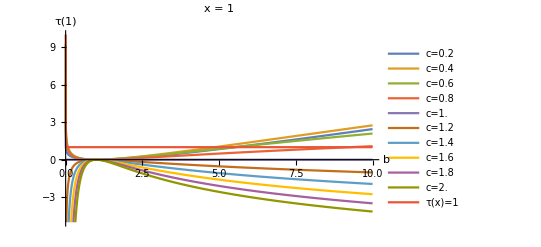

```mathematica
x=1;
n=10;

Clear[b, c]

tauvals[x_, c_, b_]:= c*Log[b]*(b^(1-c*x)-1)

cvalues=N[(2*Range[1,n])/10];
legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"c=",ToString[cvalues[[i]]]}]]
]
legends=Append[legends, "τ(x)=1"];

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[x, cvalues[[i]], b]]
]
out=Append[out, 1];

Plot[
out,
{b, 0,10},
PlotRange->{-5, 10},
PlotLegends-> legends,
AxesLabel-> {Style["b", 12],Style[StringJoin["τ(",ToString[x], ")"], 12] },
PlotLabel->StringJoin["x = ", ToString[x]]
]
```

The curves above y=0 are associated with values of c less than 1/x.
The curves below y=0 are associated with values of c more than 1/x.
The green curve on y=0 is associated with c=1/x.
Here x=1 in the two plots above.

Let’s modify the plot such that x is small:

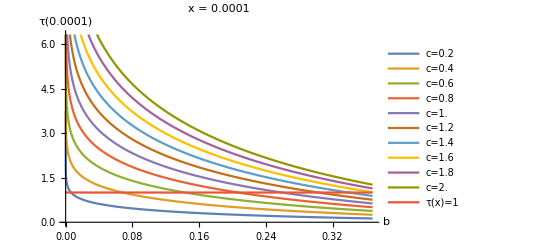

```mathematica
x=0.0001;
n=10;

Clear[b, c]

tauvals[x_, c_, b_]:= c*Log[b]*(b^(1-x*c)-1)

xvalues=N[(2*Range[1,n])/10];
legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"c=",ToString[cvalues[[i]]]}]]
]
legends=Append[legends, "τ(x)=1"];

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[x, cvalues[[i]], b]]
]
out=Append[out, 1];

Plot[
out,
{b, 0,1/ⅇ},
PlotLegends-> legends,
AxesLabel-> {Style["b", 12],Style[StringJoin["τ(",ToString[x], ")"] , 12]},
PlotLabel->StringJoin["x = ", ToString[x]]
]
```

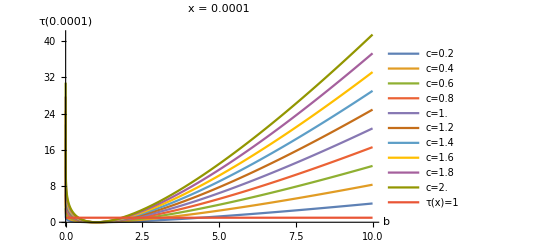

```mathematica
x=0.0001;
n=10;

Clear[b, c]

tauvals[x_, c_, b_]:= c*Log[b]*(b^(1-x*c)-1)

xvalues=N[(2*Range[1,n])/10];
legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"c=",ToString[cvalues[[i]]]}]]
]
legends=Append[legends, "τ(x)=1"];

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[x, cvalues[[i]], b]]
]
out=Append[out, 1];

Plot[
out,
{b, 0,10},
PlotLegends-> legends,
AxesLabel-> {Style["b", 12],Style[StringJoin["τ(",ToString[x], ")"], 12] },
PlotLabel->StringJoin["x = ", ToString[x]]
]
```

The smaller the value of c, the lower the position of the curve. The blue line at the bottom corresponds to c=0.1.

For 0<c<1/x we see that for a given value of c there is a minimum valid value of b. This is a little worrying, as we want small values of b (the minimum value of our output). There is also a maximum value of b, but this seems to be outside the region.

It follows that for a given value of b, we need to compute the constraints on c.

We can’t express c as a function of b, because the constraint function includes the form c ⅇ^cas well as b log(b). Neither of those forms can be reduced with elementary functions, as the solution is a Lambert W function (see note). Instead we will have to calculate the constraints on c numerically for a given value of b.

We do observe from these plots, that for small values of c and small values of x, the lower constraint on b is quite small. Let’s get a better sense of how small with a log-log plot and smaller values of c:

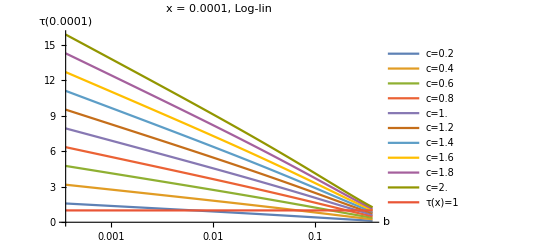

```mathematica
x=0.0001;
n=10;

Clear[b, c]

tauvals[x_, c_, b_]:= c*Log[b]*(b^(1-x*c)-1)

xvalues=N[(2*Range[1,n])/10];
legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"c=",ToString[cvalues[[i]]]}]]
]
legends=Append[legends, "τ(x)=1"];

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[x, cvalues[[i]], b]]
]
out=Append[out, 1];

LogLinearPlot[
out,
{b, 0,1/ⅇ},
PlotLegends-> legends,
AxesLabel-> {Style["b", 12],Style[StringJoin["τ(",ToString[x], ")"] , 12]},
PlotLabel->StringJoin["x = ", ToString[x], ", Log-lin"]
]
```

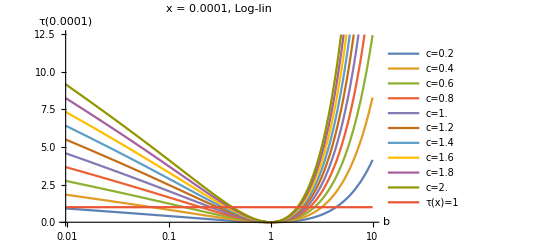

```mathematica
x=0.0001;
n=10;

Clear[b, c]

tauvals[x_, c_, b_]:= c*Log[b]*(b^(1-x*c)-1)

cvalues=N[(2*Range[1,n])/10];
legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"c=",ToString[cvalues[[i]]]}]]
]
legends=Append[legends, "τ(x)=1"];

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[x, cvalues[[i]], b]]
]
out=Append[out, 1];

LogLinearPlot[
out,
{b, -1,10},
PlotLegends-> legends,
AxesLabel-> {Style["b", 12],Style[StringJoin["τ(",ToString[x], ")"] , 12]},
PlotLabel->StringJoin["x = ", ToString[x], ", Log-lin"]
]
```

#### (Numeric optimization)?

The way forward is to solve τ(x; b, c)=1 for c given a value of b, to find the range of c where τ(x; b, c)<1.

τ(x; b, c):=c log(b)( b^(1-c x)-1)<1

The way forward is to solve τ(x; b, c)=1 for c given a value of b, to find the range of c where τ(x; b, c)<1.

τ(x; b, c):=c b log(b)(ⅇ -b^(-c x))<1

Given conditions b>0, x>0:

c b log(b)(ⅇ -b^(-c x))<1

b log(b)(c ⅇ -c b^(-c x))<1

(c ⅇ -c b^(-c x))<1/(b log(b)) for b log(b)>0⇔b>1

(c ⅇ -c b^(-c x))>1/(b log(b)) for b log(b)<0⇔0<b<1

We can’t solve this inequality analytically:

```mathematica
Clear[x, b, c]
b = 0.2;
Solve[c*E-c*b^(-c*x)==1/(b *Log[b]), c, Reals, Assumptions->{x>0, x<1}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[ⅇ c-c 0.2^(-c x)==-3.10667,c,ℝ,Assumptions→{x>0,x<1}]

```mathematica
Clear[x, b, c]
```

```mathematica
Solve[c*b*Log[b]* (E-b^(-c* x))<1, c, Reals, Assumptions->x>0]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[b c log(b) (ⅇ-b^(-c x))<1,c,ℝ,Assumptions→x>0]

WolframAlphaQueryNoResults

The strategy is to solve (c ⅇ -c b^(-c x))>1/(b log(b))for c with two extreme values of x.

First, we set x to 0:

```mathematica
Clear[x,b,c]
b=1.2;
x=0;
NSolve[c*E-c*b^(-c*x)==1/(b*Log[b]),c,Reals]
```

{{c→2.66003}}

Then, we set x to a very high number which is effectly ∞. We find that x=1000000 is a reasonable extreme value:

```mathematica
Clear[x,b,c]
b=1.2;
x=1000000;
NSolve[c*E-c*b^(-c*x)==1/(b*Log[b]),c,Reals]
```

{{c→-0.0000615171},{c→1.68146}}

We abandon the negative solution.

If 0<b<1, c should be greater than the calculated threshold.
 If b<1, c should be less than the calculated threshold (and greater than 0).

Generate an exponential sequence of m x-values between 0 and 1, then 1, then m values above 1, all prepended by 0. E.g. (0, 0.01, 0.1, 1, 10, 100). A total of n=2*m+2 numbers.

Generate an exponential sequence of m x-values between 0 and 1, then 1, then m values above 1, all prepended by 0. E.g. (0, 0.01, 0.1, 1, 10, 100). A total of n=2*m+2 numbers.

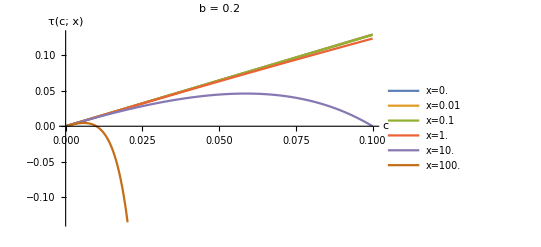

```mathematica
b = 0.2;
m=2; 
n=2*m+2;

Clear[c, x]

tauvals[x_, c_, b_]:= c*Log[b]*(b^(1-x*c)-1)

xvalues=N[Flatten[Append[{0}, 10^(Range[-m,m])]]];
legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"x=",ToString[xvalues[[i]]]}]]
]

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[xvalues[[i]], c, b]]
]

Plot[
out,
{c, 0, 0.1},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->legends,
PlotLabel->StringJoin["b = ", ToString[b]]
]
```

```mathematica
n=10;

Clear[c, x]

tauvals[x_, c_, b_]:= c*b*Log[b]*(E-b^(-c x))

xvalues=N[Range[1, n]/10];

legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"x=",ToString[xvalues[[i]]]}]]
]

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[xvalues[[i]], c, b]]
]

Plot[
out,
{c, 0, 4},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLabel->StringJoin["b = ", ToString[b]],
PlotLegends->legends,
PlotRange->{-1, 1}
]
```

-Graphics-

τ(x; b, c)  is not monotonically increasing in c.

So for which value of x should we solve τ(x; b, c) for c?

For positive values of τ(x; b, c), τ(x; b, c)is increasing in c.

Since we have an upper constraint on τ(x; b, c), the “worst case” is x=∞.

τ( x; b, c ) is increasing as c is increasing, when x > 1. This is true for all b > 0.
For all other values of x, τ( x; b, c) is not monotonically increasing in c.

So for which value of x should we solve τ(x; b, c) for c?

Since we have an upper constraint on τ(x; b, c), the “worst case” is x=0.

Let’s define τ(c):=τ(c; x, b)|_(x=0)=c log(b) (b-1)

Let’s define τ(c):=τ(c; x, b)|_(x = ∞)=c b log(b)ⅇ 
for c>0.

Here we are imposing the constraint c>0, to simplify the problem.

```mathematica
tau2[b_, c_]:= c * Log[b]*(b-1)
```

```mathematica
tau2[b_, c_]:= c * b*Log[b]*E
```

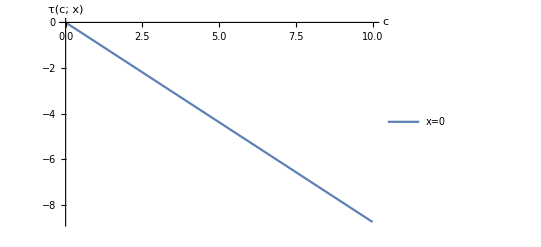

```mathematica
b = 0.2;
Plot[
{
tau2[b, c]
},
{c, 0, 10},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->{"x=0"}
]
```

#### For b>1:

Let’s first consider the case b>1:

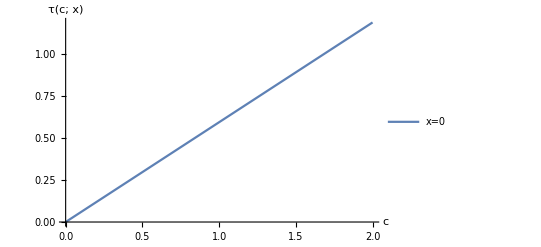

```mathematica
Clear[b, c]
b = 1.2;
Plot[
{
tau2[b, c]
},
{c, 0, 2},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->{"x=0"}
]
```

```mathematica
b=1.2;
NSolve[tau2[b, c]==1, c]
```

{{c→1.68146}}

It looks about right, that for b=1.2, τ(x; c)=1 when c=1.68.

```mathematica
b=0.2;
NSolve[tau2[b, c]==1, c]
```

{{c→-1.14288}}

Of course, with x=0, it is easy to solve for c analytically:

Of course, with x=0, it is easy to solve for c analytically:

τ(c):=τ(c; x, b)|_(x = ∞)=c b log(b)ⅇ<1

⇔c<1/(b log(b)ⅇ)

for b>1.

c log(b) (b-1)<1⟺c<1/(log(b) (b-1))
Note that log(b)<0  and b-1<0, when 0<b<1/ⅇ.

#### For 0<b<=1:

```mathematica
Clear[b, c]
b = 0.2;
Plot[
{
tau2[b, c]
},
{c, 0, 10},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->{"x=0"}
]
```

-Graphics-

For b=1:

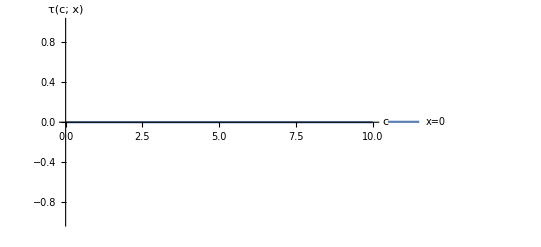

```mathematica
Clear[b, c]
b = 1;
Plot[
{
tau2[b, c]
},
{c, 0, 10},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->{"x=0"}
]
```

The point here is, that c>0 is the only constraint on c for 0<b<=1.

The tricky part is that we don’t know if τ(x) is increasing in x. So we don’t know if the constrains for the lower extreme (x=0) or the higher extreme (x=∞) apply.

```mathematica
Clear[x, c, b]

δ=1*^-12;
cmax=10;

f6[x_, b_, c_]:=1/( Exp[Log[b]*(c * x-1)])+(c*Log[b]+1)*x
g6[x_]:=x
h6[x_, b_, c_]:=Piecewise[{{f6[x, b, c], x<1/c},{g6[x], x>=1/c}}]

Manipulate[
LogLogPlot[
h6[x, b, c], 
{x, 0,100}, 
PlotRange->{0, 100},
PlotLegends->{"h(x)"},
AxesLabel->{"x", "h(x)"}
],
{{b, 0.1}, δ, 2, Appearance->"Open"},
{{c, 0.1}, δ, If[b>1, 1/(b *Log[b]* E), cmax], Appearance->"Open"}
]
```

#### Conclusion for region 1 (0<b<1/ⅇ)

Constraint:
c<1/(log(b) (b-1))

If we constrain c to c<1/(log(b) (b-1)), when 1/ⅇ<b<1, we should be safe for all positive x.

### Region 2: 1/ⅇ<=b<=1

-1<=log(b)<=0⟺1/ⅇ<=b<=1

If log(b)=0, then we get the constraint
τ(x; b, c):=c log(b)( b^(1-c x)-1)=0<1

...which is true for all c.

If -1<=log(b)<0, then...
 τ(x; b, c):=c log(b)( b^(1-c x)-1)<1 only if ...??

Picking a b-value inside the region, very close to the lower bound:

Generate a sequence of x-values:
x_exp={10^(-m),..., 10^(-1)}
x_lin={1, ..., 10}/10
x_vals={x_exp, x_lin}

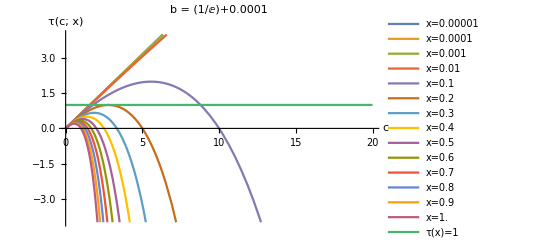

```mathematica
b = (1/ⅇ)+0.0001;
m=5; 

n=m+9;

Clear[c]

tauvals[x_, c_, b_]:= c Log[b](b^(1-c * x)-1)

xvalues=N[Flatten[Append[
10^(Range[-m,-1]),
Range[2, 10]/10
]]];
legends={};
For[
i=1, i<n+1, i++, legends=Append[legends,StringJoin[{"x=",ToString[xvalues[[i]]]}]]
]
legends=Append[legends, "τ(x)=1"];

out={};
For[
i=1, i<n+1, i++, out=Append[out,tauvals[xvalues[[i]], c, b]]
]
out=Append[out, 1];

Plot[
out,
{c, 0, 20},
PlotRange->{-4, 4},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->legends,
PlotLabel->"b = (1/ⅇ)+0.0001"
]
```

Again, let’s consider the extreme case where x=0.

Then we have the constraint
τ(x; b, c):=c log(b)( b^(1-c x)-1)=c log(b) (b-1)<1

Here we have 
c>0
-1<log(b)<0
1/ⅇ-1<b-1<0

So log(b) (b-1) is positive for 1/ⅇ<b<1. Therefore,
c<1/(log(b) (b-1))

What if b=1?

The theoretical maximum value of c is ∞ for b=1. Also, for values of b close to 1 we will get huge maximum values of c (which of course in itself should not be a problem).

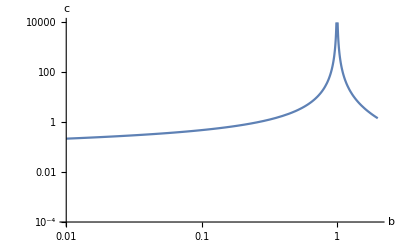

```mathematica
LogLogPlot[
1/(Log[b]*(b - 1)), 
{b, 0.01, 2}, 
PlotRange->{1*^-4, 1*^4},
AxesLabel-> {"b", "c"}
]
```

So when implementing the function it may be necessary to implement som kind of practical maximum c value, as in the plot below, where the range fo the slider for the c value is calculated automatically based on the chosen b value. 10 might be a sensible maximum value for a c slider.

#### Conclusion for region 2 (1/ⅇ<b<1)

Constraint:
c<1/(log(b) (b-1))

If we constrain c to c<1/(log(b) (b-1)), when 1/ⅇ<b<1, we should be safe for all positive x.

### Region 3: 1<b<ⅇ

0<=log(b)<1⟺1<b<ⅇ

If log(b) = 1, then b=ⅇ, and we get the constraint...
τ(x; b, c):=c log(b)( b^(1-c x)-1)=c(ⅇ^(1-cx)-1)<1

Let’s get a visual of the situation. Define
τ(c; x):=c(ⅇ^(1-cx)-1)

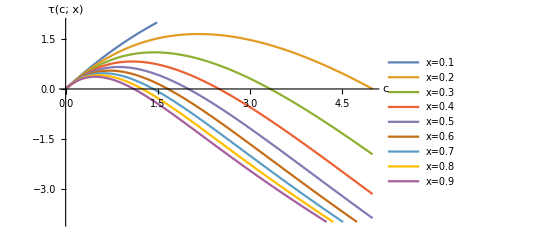

```mathematica
Plot[
{c(Exp[1-c* 0.1 ]-1),
c(Exp[1-c* 0.2]-1),
c(Exp[1-c* 0.3]-1),
c(Exp[1-c* 0.4]-1),
c(Exp[1-c* 0.5]-1),
c(Exp[1-c* 0.6]-1),
c(Exp[1-c* 0.7]-1),
c(Exp[1-c* 0.8]-1),
c(Exp[1-c* 0.9]-1)
},
{c, 0, 5},
PlotRange-> {-4, 2},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->{
"x=0.1",
"x=0.2",
"x=0.3",
"x=0.4",
"x=0.5",
"x=0.6",
"x=0.7",
"x=0.8",
"x=0.9"
}
]
```

For small values of x we risk hitting the constraint. Again, we need to deal with this, as the situation where we need the limiter function is exactly when x is small.

So again, let’s look at the extreme case where x=0:

c(ⅇ^(1-cx)-1)<1
ⅇ^(1-cx)=ⅇ when x=0. So we get the constraint
c(ⅇ-1)<1⟺c<1/(ⅇ-1)≈0.581977

```mathematica
1/(E - 1)//N
```

0.581977

f(0.58)=1 looks about right:

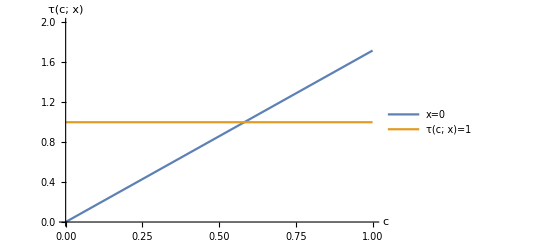

```mathematica
Clear[c]

Plot[
{c(Exp[1]-1),
1
},
{c, 0, 1},
PlotRange-> {0, 2},
AxesLabel->{Style["c", 12],Style["τ(c; x)", 12]},
PlotLegends->{"x=0", "τ(c; x)=1"}
]
```

For 1<b<ⅇ the situation is the same as before:

Log(b) (b-1) is positive. Therefore, as before
c<1/(log(b) (b-1))

#### Conclusion for region 3 (1<b<ⅇ)

Constraint:
c<1/(log(b) (b-1))

If we constrain c to c<1/(log(b) (b-1)), when 1<b<ⅇ, we should be safe for all positive x.

### Region 4: b>=e

log(b)>=1⟺b>=e

Above we considered the case where b=ⅇ. Now let’s focus on the case where b>ⅇ.

Again we look at the constraint:
τ(x; b, c):=c log(b)( b^(1-c x)-1)<1

Here, 
c>0
b>ⅇ>1
log(b)>1>0
x>0 by definition

For b>ⅇ the situation is again the same as before:

Log(b) (b-1) is positive. Therefore, as before

c<1/(log(b) (b-1))

#### Conclusion for region 4 (b>ⅇ)

Constraint:
c<1/(log(b) (b-1))

If we constrain c to c<1/(log(b) (b-1)), when b>1, we should be safe for all positive x.